```mathematica
Quit[]
```

```mathematica
mode=1;
```

#### Load solution

```mathematica
SetDirectory[NotebookDirectory[]]
Needs["spectral`","../spectral.m"];
```

/Users/rekierj/sprouts/multilayer

```mathematica
vector=LinearSolve[Sprouts`Amat[0],Sprouts`bvec];
```

```mathematica
vector=feigv[[mode]];
val=feig[[mode]];
```

```mathematica
Sprouts`nr=First@Sprouts`n;
ClearAll[sollayer]
list=Sprouts`nr*Length/@Sprouts`layout;
If[True,list[[1]]/=2];
sublists=TakeList[vector,list];
MapIndexed[(sollayer[First@#2]=#1)&,sublists];
```

```mathematica
out=Table[
If[i==1,
AssociationThread[Sprouts`layout[[i]],Riffle[#,0.+0.ⅈ]&/@Partition[sollayer[i],Sprouts`nr/2]],
AssociationThread[Sprouts`layout[[i]],Partition[sollayer[i],Sprouts`nr]]
]
,{i,1,Length[Sprouts`layout]}]//Join//Association;
outnull=Map[(#)->ConstantArray[0,Sprouts`nr]&,Keys[out]/.f_[ℓ_,𝓂_]->f[ℓ-1,𝓂]]~Join~Map[(#)->ConstantArray[0,Sprouts`nr]&,Keys[out]/.f_[ℓ_,𝓂_]->f[ℓ+1,𝓂]];
(*AppendTo[out,outnull];*)
```

```mathematica
ClearAll[NChebevalC,xk,rk]
NChebevalC[c_][x_]:=NChebeval[N[Re[c]]][x]+ⅈ NChebeval[N[Im[c]]][x]
xk=Join[{1},Cos[((2Range[1,Sprouts`nr]-1)π)/(2Sprouts`nr)],{-1}]//N;
intervals={};
Table[
rk[layer]=Sprouts`rfu[layer][xk];
AppendTo[intervals,Max[rk[layer]]];
,{layer,1,Length[Sprouts`layout]}];
```

#### Plot solution

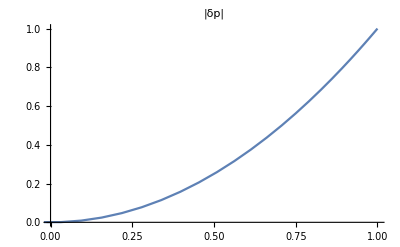

```mathematica
(* plot chosen component *)
ClearAll[data]
With[{ℓ=2,𝓂=2},
data[1]=NChebevalC[Δp[ℓ,𝓂]/.out][xk]//Chop;
plotp=Show[Sequence@Table[
ListPlot[{{rk[layer],Abs[data[layer]]}ᵀ},Joined->True,PlotMarkers->None(*Automatic*)]
,{layer,1,1}],PlotRange->{{0,1},Automatic},Epilog->{Dashed,Line[{{#,-1},{#,1}}]&/@Most@intervals},PlotLabel->"|δp|"]
]
```

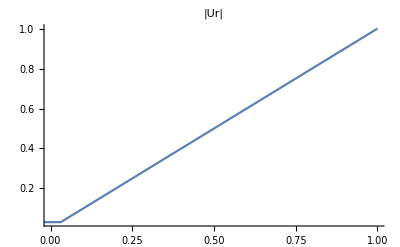

```mathematica
(* plot chosen component *)
ClearAll[data]
With[{ℓ=2,𝓂=2},
data[1]=ℓ(ℓ+1)(NChebevalC[P[ℓ,𝓂]/.out][xk])/rk[1]//Chop;
plotUr=Show[Sequence@Table[
ListPlot[{{rk[layer],Abs[data[layer]]}ᵀ},Joined->True,PlotMarkers->None (*Automatic*)]
,{layer,1,1}],PlotRange->{{0,1},All},Epilog->{Dashed,Line[{{#,-1},{#,1}}]&/@Most@intervals},PlotLabel->"|Ur|"]
]
```

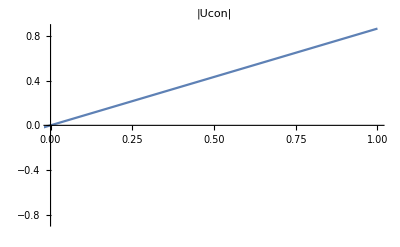

```mathematica
(* plot chosen component *)
ClearAll[data]
With[{ℓ=2,𝓂=2},
data[1]=√((ℓ(ℓ+1))/2)(NChebevalC[DCheb[P[ℓ,𝓂]/.out]][xk]+(NChebevalC[P[ℓ,𝓂]/.out][xk])/rk[1])//Chop;
plotUcon=Show[Sequence@Table[
ListPlot[{{rk[layer],Re[data[layer]]}ᵀ},Joined->True,PlotMarkers->None(*Automatic*)]
,{layer,1,1}],PlotRange->{{0,1},All},Epilog->{Dashed,Line[{{#,-1},{#,1}}]&/@Most@intervals},PlotLabel->"|Ucon|"]
]
```

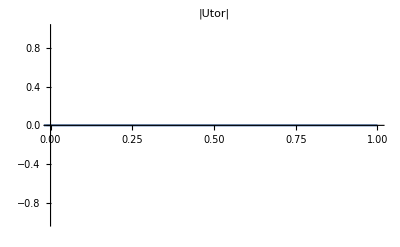

```mathematica
(* plot chosen component *)
ClearAll[data]
With[{ℓ=3,𝓂=2},
(*data[1]=√((ℓ(ℓ+1))/2)(NChebevalC[c1f[ℓ,𝓂]/.out][xk])/rk[1]//Chop;*)
data[1]=√((ℓ(ℓ+1))/2)(ⅈ NChebevalC[T[ℓ,𝓂]/.out][xk])//Chop;
(*data[3]=√((ℓ(ℓ+1))/2)((NChebevalC[c3f[ℓ,𝓂]/.out][xk])/rk[3])//Chop;*)
plotUtor=Show[Sequence@Table[
ListPlot[{{rk[layer],Abs[data[layer]]}ᵀ},Joined->True,PlotMarkers->None(*Automatic*)]
,{layer,1,1}],PlotRange->{{0,1},All},Epilog->{Dashed,Line[{{#,-1},{#,1}}]&/@Most@intervals},PlotLabel->"|Utor|"]
]
```

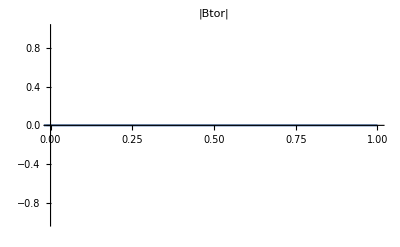

```mathematica
(* plot chosen component *)
ClearAll[data]
With[{ℓ=2,𝓂=2},
(*data[1]=√((ℓ(ℓ+1))/2)(NChebevalC[c1f[ℓ,𝓂]/.out][xk])/rk[1]//Chop;*)
data[1]=√((ℓ(ℓ+1))/2)(ⅈ NChebevalC[G[ℓ,𝓂]/.out][xk])//Chop;
(*data[3]=√((ℓ(ℓ+1))/2)((NChebevalC[c3f[ℓ,𝓂]/.out][xk])/rk[3])//Chop;*)
plotUtor=Show[Sequence@Table[
ListPlot[{{rk[layer],Abs[data[layer]]}ᵀ},Joined->True,PlotMarkers->None(*Automatic*)]
,{layer,1,1}],PlotRange->{{0,1},All},Epilog->{Dashed,Line[{{#,-1},{#,1}}]&/@Most@intervals},PlotLabel->"|Btor|"]
]
```